{-Graphics-,-Graphics-}

11.7881+1.89853 x

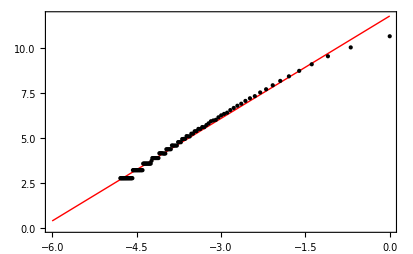

{-Graphics-,-Graphics-}

13.0242+1.69349 x

-Graphics-

```mathematica
img=-Graphics-(*-Graphics--Graphics-;*);
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];
data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```